# Course 2 Axiomatic Foundation of Probability

## Statistical Experiment ⇒ Sample Space

## P : B → ℝ_+ , B ⊂2^Ω

P (ϕ) = 0, P (Ω) = 1

P (A) ≥ 0, A ⊂ B

Countable Additivity

```mathematica
P(∪_(n=1)^∞Subscript[A, k])=∑_(n=1)^∞ P(Subscript[A, k]),Subscript[A, i]∩Subscript[A, j]=ϕ,∀i,j

A⊂B,P(A)≤P(B)=P(A)+P(B\A)≥P(A)

Subscript[A, n]↑A,Subscript[A, 1]⊂Subscript[A, 2]⊂…⊂Subscript[A, n],lim_(n->∞) Subscript[A, n]=A⇒lim_(n->∞) P(Subscript[A, n])=P(A)
Subscript[A, n]=(Subscript[A, n]\Subscript[A, n-1])∪(Subscript[A, n-1]\Subscript[A, n-2])∪…∪(Subscript[A, 2]\Subscript[A, 1])∪Subscript[A, 1]
P(Subscript[A, n])=(∑_(k=1))^n P(Subscript[A, k]\Subscript[A, k-1]),Subscript[A, 0]=ϕ,lim_(n->∞) P(Subscript[A, n])=P(A)
```

## Inclusive-Exclusive Rule

```mathematica
P(A∪B)=P(A)+P(B)-P(A∩B)
```

To prove :

```mathematica
P((∪_(k=1))^n Subscript[A, k])≤(∑^n)_(k=1)P(Subscript[A, k])
```

Proof :

```mathematica
n=2,P(A∪B)=P(A)+P(B)-P(A∩B)≤P(A)+P(B)
```

Assume that :

```mathematica
P((∪^n)_(k=1)Subscript[A, k])≤(∑^n)_(k=1)P(Subscript[A, k])(Boole Inequality)
```

Then :

```mathematica
P((∪^(n+1))_(k=1)Subscript[A, k])=P(((∪^n)_(k=1)Subscript[A, k])∪Subscript[A, n+1])=P((∪^n)_(k=1)Subscript[A, k])+P(Subscript[A, n+1])-P(((∪^n)_(k=1)Subscript[A, k])∩Subscript[A, n+1])≤(∑^n)_(k=1)P(Subscript[A, k])+P(Subscript[A, n+1])≤(∑^(n+1))_(k=1)P(Subscript[A, k]).□
```

```mathematica
P((∪^n)_(k=1)Subscript[A, k])=∑_(k=1)^n P(Subscript[A, k])-∑_(i<j) P(Subscript[A, i]∩Subscript[A, j])+∑_(i<j<k) P(Subscript[A, i]∩Subscript[A, j]∩Subscript[A, k])-…+(-1)^n P(∩_(k=1)^n Subscript[A, k])    (Dependence)
```

### Matching Problem

```mathematica
Subscript[A, k]⊂Ω,{kth,right}
```

```mathematica
By Inclusive-Exclusive Rule: P(Subscript[A, 1]∪Subscript[A, 2]∪…∪Subscript[A, n])=1/n({{n}, {1}})-1/(n(n-1))({{n}, {2}})+…+(-1)^(n+1)1/(n!)({{n}, {n}})=1-1/(2!)+…+(-1)^(n+1)1/(n!)
```

```mathematica
Noting that: e^x=∑_(k=0)^∞ x^k/(k!)
Thus: lim_(n->∞) P(Subscript[A, 1]∪Subscript[A, 2]∪…∪Subscript[A, n])=1-1/e
```

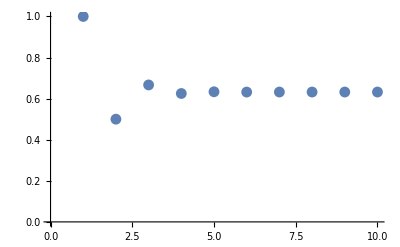

```mathematica
ListPlot[Table[Sum[(-1)^(k+1)/(k!),{k,1,n}],{n,1,10}],PlotRange->All]
```

## Non-Measurable Set

```mathematica
P:B->SubPlus[ℝ],B⊂2^Ω,Ω=ℝ
```

```mathematica
Vitali Set
```

```mathematica
Equivalent Relation
```

```mathematica
Construction of a Vitali set S:
```

```mathematica
Q={Subscript[r, 1],Subscript[r, 2],…,Subscript[r, n],…} is the rational numbers
S⊂[0,1],
∀x∈[0,1],∃!v∈S,s.t.v-x=Subscript[r, k]∈Q
Def: x⊕y=x+y mod 1={{{x+y,      x+y≤1}, {x+y-1,x+y>1}}
∪_(k=1)^∞S⊕Subscript[r, k]=[0,1]
(S⊕Subscript[r, i])∩(S⊕Subscript[r, j])=ϕ
```

```mathematica
P([0,1])=P(∪_(k=1)^∞S⊕Subscript[r, k])=∑_(k=1)^∞ P(S⊕Subscript[r, k])=∑_(k=1)^∞ P(S)
```

## Algebra

### Set Class : 𝒜 ⊂ 2^Ω

### Algebra

```mathematica
𝒜⊂2^Ω
```

```mathematica
Properties:
```

```mathematica
1. A∈𝒜⇒A^C∈𝒜
```

```mathematica
2. A∈𝒜,B∈𝒜⇒A∪B∈𝒜
```

### e. g.

```mathematica
Ω=[0,1],P((a,b))=b-a,P((a,b)∪(c,d))=b-a+d-c if (a,b)∩(c,d)=∅
P((a,b])=P((∪_(k=1))^∞(a,b+1/k))=lim_(k->∞) (b+1/k-a)=b-a
```

### σ - Algebra

```mathematica
ℬ⊂2^Ω
```

```mathematica
Properties:
```

```mathematica
1. A∈ℬ⇒A^C∈ℬ
```

```mathematica
2. Subscript[A, k]∈ℬ⇒(∪_(k=1))^∞Subscript[A, k]∈ℬ
```

### Borel Set

```mathematica
𝒜={(-∞,x],x∈ℝ}⇒σ(𝒜)
```

```mathematica
(a,b]=(-∞,b]\(-∞,a]
(a,b)=(∪_(k=1))^∞(a,b-1/k]
{x}=(-∞,x]\(-∞,x)
```

```mathematica
P((-∞,a]),Ω=[0,1]
P([0,x])=x⇒P([0,x))=x
P({x})=0⇒P(Q)=0
```

```mathematica
(Ω,ℬ,P)
```

```mathematica
Probability Triple
```

```mathematica
Kolmogorov
```